```mathematica
ϵ = 1.*8065.5 (*100*);
α =N[400/π] (*(0.05 ϵ)/π*)(*10/3.14*);
ω0 =500 ;
wc =53  (*0.1 ϵ*);
Γ = N[ω0^2/wc]; (* Width of distribution *)
Temp = 300;
kB = 0.695;
```

```mathematica
ρ00i = 0.5;
ρ01i = 0.5;
ρ10i = 0.5;
ρ11i= 0.5;
```

```mathematica
β =1/(kB Temp)(*0.95/ϵ *)(**)
```

0.00479616

```mathematica
J[ω_, α_]:= (α Γ ω0^2 ω)/((ω0^2 - ω^2)^2 + Γ^2 ω^2) (**)

Jod[ω_, α_] :=  (α ω wc)/(ω^2+wc^2)
```

```mathematica
w0List = {200, 400, 600}
```

{200,400,600}

```mathematica
Plot
```

Plot

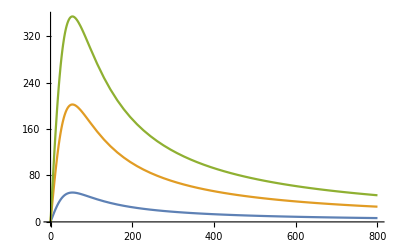

```mathematica
Plot[{J[ω, 100],J[ω, 400], J[ω, 700]},{ω,0,800}, PlotRange->Automatic]
```

```mathematica
(*S1:= -4 NIntegrate[J[ω]/ω^2 Coth[ω/(2 kB Temp)], {ω, 0, 10wc}, Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->30 ]*)
S[t_]:=- NIntegrate[J[ω]/ω^2 Coth[(ω β)/2] (1-Cos[ω t]), {ω, 0, ω0+10wc}, Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->40 ]
```

```mathematica
rho10[t_] := ρ10i Exp[S[t]] Exp[ⅈ ϵ t]
 rho01[t_] := ρ01i Exp[S[t]] Exp[-ⅈ ϵ t]
```

```mathematica
t0 = 0; tf= 100/ϵ; di =(tf-t0)/2000;
tlist = N[Range[t0,tf, di]];
ListPlot[Transpose@{tlist, Re@rho01[tlist]}, PlotRange->All]
ListPlot[Transpose@{tlist, Im@rho01[tlist]}, PlotRange->All]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::inumr: The integrand (1 - Cos[6.19924×10^-6\ ω])\ Coth[0.00239808\ ω]\ J[ω]/ω^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1030}}.

NIntegrate::inumr: The integrand (1 - Cos[0.0000123985\ ω])\ Coth[0.00239808\ ω]\ J[ω]/ω^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1030}}.

NIntegrate::inumr: The integrand (1 - Cos[0.0000185977\ ω])\ Coth[0.00239808\ ω]\ J[ω]/ω^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1030}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

```mathematica
data=Transpose@{tlist, Re@rho01[tlist]};
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
Directory[]
```

/Users/henrymaguire

```mathematica
Export["Work/phd-work/vibronic-TLS/DATA/Exactdata.dat",data]
```

Work/phd-work/vibronic-TLS/DATA/Exactdata.dat